Your Title Here

```mathematica
P=1;(*bar*)
Psat1[temp_]:=10^(5.31301-1676.569/(temp+251.272));(*methanol*)
Psat2[temp_]:=10^(4.6542-1435.264/(temp+208.152));(*water*)
```

```mathematica
A12=0.7923;A21=0.5434;
γ1[x_]:=Exp[(1-x)^2*(A12+2*(A21-A12)*x)];
γ2[x_]:=Exp[x^2*(A21+2*(A12-A21)*(1-x))];
```

```mathematica
equilb=Quiet@Interpolation[{#,y/.Quiet@FindRoot[{y==(#*γ1[#]*Psat1[temp])/P,P==#*γ1[#]*Psat1[temp]+(1-#)*γ2[#]*Psat2[temp]},{{y,0},{temp,100}}]}&/@Range[0,1,0.05]];
```

```mathematica
xybase=Plot[{equilb[x],x},{x,0,1},PlotStyle->{{Thick,Black}},PlotRange->{{0,1},{0,1}},
Frame->True,FrameLabel->{"liquid mole fraction","vapor mole fraction"},LabelStyle->{17,Black},AspectRatio->Full,PlotRangeClipping->False];
```

```mathematica
Manipulate[
Module[{zf,xd,xb,R,feed,rect,xi,yi,Vb,strip,i,yR,xR,x1,y1,nR,yS,xS,nS,nT,Ry,Rx,Sy,Sx,reboiler,lines,diagram},
zf=0.5;xd=0.85;xb=0.05;R=1.5;
feed[x_]:=q/(q-1)*x-zf/(q-1);

rect[x_]:=R/(R+1)*x+xd/(R+1);
xi=x/.Quiet@FindRoot[feed[x]==rect[x],{x,0.7}];yi=rect[xi];

Vb=(xb-xi)/(xi-yi);
strip[x_]:=(Vb+1)/Vb*x-1/Vb*xb;

(*RECTIFYING*)
i=0;yR[0]=xd;xR[0]=xd;
While[xR[i]>xi,{
x1=x/.Quiet@FindRoot[yR[i]==equilb[x],{x,0.7}],
y1=rect[x1],
If[x1>xi,{xR[i+1]=x1,yR[i+1]=y1}],
i++}];
nR=i-1;

(*STRIPPING*)
i=0;yS[0]=yR[nR];xS[0]=xR[nR];
While[xS[i]>xb,{
x1=x/.Quiet@FindRoot[yS[i]==equilb[x],{x,0.5}],
y1=strip[x1],
xS[i+1]=x1,
yS[i+1]=y1,
i++}];
nS=i-1;
nT=nR+nS+1;
(*If[step>nT,step=nT+1];*)

(*R STAGES*)
Ry=Line[{{xR[#],yR[#-1]},{xR[#],yR[#]}}]&/@Range@nR;
Rx=Line[{{xR[#],yR[#]},{xR[#+1],yR[#]}}]&/@If[nR≥1,Range[0,nR-1],{0}];
(*S STAGES*)
Sy=Line[{{xS[#+1],yS[#]},{xS[#+1],yS[#+1]}}]&/@Range[0,nS-1];
Sx=Line[{{xS[#-1],yS[#-1]},{xS[#],yS[#-1]}}]&/@Range[nS+1];
reboiler=Line[{{xS[nS],yS[nS]},{xS[nS+1],yS[nS]},{xS[nS+1],xS[nS+1](*yS[nS+1]*)}}];

lines=Show[
Plot[feed[x],{x,xi,zf},PlotStyle->{Thick,Blue}],
Plot[rect[x],{x,xi,xd},PlotStyle->{Thick,RGBColor[1,0.4,0]}],
Plot[strip[x],{x,xb,xi},PlotStyle->{Thick,Hue@0.9}],
Graphics[{
Thick,Insert[Take[Join[{Text@""},Partition[Riffle[Rx,Ry],2],Partition[Riffle[Sx,Sy],2],{reboiler},ConstantArray[Text@"",5]],step],RGBColor[0,0.6,0],step],
Take[DeleteCases[Flatten@{Text@"",
Text[Style[(*nT-#*)#,18],{xR[#],yR[#-1]},{1,-1}]&/@Range@nR,(*R stages*),
Text[Style[(*nT-nR-#*)nR+#,18],{xS[#],yS[#-1]},{1,-1}]&/@Range@nS,(*S stages*)
Text[Style["R",18,Italic,Background->White],{xS[nS+1],yS[nS]},{1,-1}],
ConstantArray[Text@"",5]
},Null],step],
If[step>1,Text[Style[Column[{Row@{"total stages = ",nT},Framed[Column[{
Row@{"rectifying = ",nR},Row@{"stripping = ",nS},Row@{"reboiler = ",1}
},Alignment->"="],FrameMargins->{{15,15},{5,5}}]
},Center],18],{0.8,0.3}]]
}]];

(*diagram=Graphics[{
{EdgeForm@Thick,FaceForm@None,Rectangle[{0,0},{1,3}],Disk[{0.75,-0.5},1.1*{0.25,0.15}],Disk[{1.75,2.8},1.1*{0.25,0.15}]},
{Thick,Arrowheads@0.07,
Arrow[{{0.5,-0.5},{0.25,-0.5},{0.25,0}}],Arrow[{{0.75,0},{0.75,-0.32}}],
{Hue@0.9,Arrow[{{1.05,-0.5},{3,-0.5}}]},
Arrow[{{0.25,3},{0.25,3.4},{1.75,3.4},{1.75,2.95}}],Arrow[{{1.5,2.8},{1,2.8}}],
{RGBColor[1,0.4,0],Arrow[{{2.05,2.8},{3,2.8}}]}},
{Text[Style[#,17],{0.5,3*#/nT},{0,-1.1}],Line[{{0,3*#/nT},{1,3*#/nT}}]}&/@Range@(nT-1)
},ImageSize->{250,400}];*)

diagram=Module[{δx1,δy1,δx2,δy2,δy3,r1,r2,size},
δx1=0.5;δy1=1;δx2=0.5;δy2=0.25;δy3=δy1/2-0.025;
r1=0.15;r2=0.07;
size=Medium;

Graphics[{Thick,
Line[{{#,-δy1/2},{#,δy1/2}}]&/@{0,δx1},
Circle[{δx1/2,δy1/2},{δy2,r1},{0,π}],Circle[{δx1/2,-δy1/2},{δy2,r1},{π,2*π}],
Arrowheads@size,
Arrow[{{δx1/2,δy1/2+r1},{δx1/2,δy1/2+r1+δy2},{δx1/2+δx2,δy1/2+r1+δy2},{δx1/2+δx2,δy1/2+r1+r2}}],
Arrow[{{δx1/2+δx2,δy1/2+r1-r2},{δx1/2+δx2,δy1/2}}],
{Arrowheads[{-size,size}],Arrow[{{δx1,δy1/2},{δx1+δx2,δy1/2}}]},
Circle[{δx1/2+δx2,δy1/2+r1},r2],
Text[Style["C",18],{δx1/2+δx2,δy1/2+r1}],

Arrow[{{δx1/2,-(δy1/2+r1)},{δx1/2,-(δy1/2+r1+0.75*δy2)},{δx1/2+0.75*δx2-r2,-(δy1/2+r1+0.75*δy2)}}],
Arrow[{{δx1/2+0.75*δx2,-(δy1/2+r1+0.75*δy2)+r2},{δx1/2+0.75*δx2,-δy1/2},{δx1,-δy1/2}}],
Arrow[{{δx1/2+0.75*δx2+r2,-(δy1/2+r1+0.75*δy2)},{δx1/2+0.75*δx2+r2+δx2/2,-(δy1/2+r1+0.75*δy2)}}],
Circle[{δx1/2+0.75*δx2,-(δy1/2+r1+0.75*δy2)},r2],
Text[Style["R",18],{δx1/2+0.75*δx2,-(δy1/2+r1+0.75*δy2)}],

{Text[Style[#,17],{δx1/2,#/nT},{0,-1.1}],Line[{{0,δy1*#/nT},{δx1,δy1*#/nT}}]}&/@Range[nT-1]
},ImageSize->{250,400}]
];

(*Show[xybase,lines,ImageSize->{600,400}]*)
Grid@{{Show[xybase,lines,ImageSize->{350,400}],diagram}}
],
Grid[{
{Control[{{npr,3,""},{1->" plot points ",2->" draw operating lines ",3->" count stages "},Setter}],Spacer@10,
Control[{{q,0.5,"feed quality"},-0.2,1.5,0.1,Appearance->"Labeled",Exclusions->1,TrackingFunction->(q=#;step=1;&)}]},
{PaneSelector[{
1->Control[{{point,1,""},{1->" feed ",2->" distillate ",3->" bottoms "},Setter}],
2->Control[{{line,2,""},{1->" feed ",2->" rectifying ",3->" stripping "},Setter}],
3->Control[{{step,1,"step off stages"},1,10,1}]
},Dynamic@npr],SpanFromLeft}
},Alignment->Left],
SaveDefinitions->True]
```

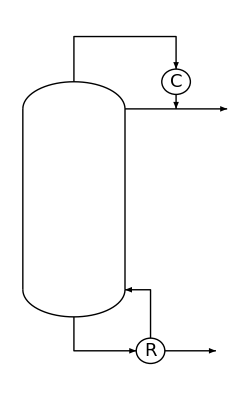





```mathematica
Module[{δx1,δy1,δx2,δy2,δy3,r1,r2,size},
δx1=0.5;δy1=1;δx2=0.5;δy2=0.25;δy3=δy1/2-0.025;
r1=0.15;r2=0.07;
size=Medium;

Graphics[{Thick,
Line[{{#,-δy1/2},{#,δy1/2}}]&/@{0,δx1},
Circle[{δx1/2,δy1/2},{δy2,r1},{0,π}],Circle[{δx1/2,-δy1/2},{δy2,r1},{π,2*π}],
Arrowheads@size,
Arrow[{{δx1/2,δy1/2+r1},{δx1/2,δy1/2+r1+δy2},{δx1/2+δx2,δy1/2+r1+δy2},{δx1/2+δx2,δy1/2+r1+r2}}],
Arrow[{{δx1/2+δx2,δy1/2+r1-r2},{δx1/2+δx2,δy1/2}}],
{Arrowheads[{-size,size}],Arrow[{{δx1,δy1/2},{δx1+δx2,δy1/2}}]},
Circle[{δx1/2+δx2,δy1/2+r1},r2],
Text[Style["C",18],{δx1/2+δx2,δy1/2+r1}],

Arrow[{{δx1/2,-(δy1/2+r1)},{δx1/2,-(δy1/2+r1+0.75*δy2)},{δx1/2+0.75*δx2-r2,-(δy1/2+r1+0.75*δy2)}}],
Arrow[{{δx1/2+0.75*δx2,-(δy1/2+r1+0.75*δy2)+r2},{δx1/2+0.75*δx2,-δy1/2},{δx1,-δy1/2}}],
Arrow[{{δx1/2+0.75*δx2+r2,-(δy1/2+r1+0.75*δy2)},{δx1/2+0.75*δx2+r2+δx2/2,-(δy1/2+r1+0.75*δy2)}}],
Circle[{δx1/2+0.75*δx2,-(δy1/2+r1+0.75*δy2)},r2],
Text[Style["R",18],{δx1/2+0.75*δx2,-(δy1/2+r1+0.75*δy2)}],
},ImageSize->{250,400}]
]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX